```mathematica
allSpectraF=Import["/Users/Tommy/Documents/UNC Charlotte/Research with Ogle/3 IA Fluorimeter and UVVis/fluorescence spectra.csv"];
ddmia=Import["/Users/Tommy/Documents/UNC Charlotte/Research with Ogle/5 Thesis/figures/ddmia.pdf"][[1]];
dpdmia=Import["/Users/Tommy/Documents/UNC Charlotte/Research with Ogle/5 Thesis/figures/dpdmia.pdf"][[1]];
dipia=Import["/Users/Tommy/Documents/UNC Charlotte/Research with Ogle/5 Thesis/figures/dipia.pdf"][[1]];
dnmia=Import["/Users/Tommy/Documents/UNC Charlotte/Research with Ogle/5 Thesis/figures/dnmia.pdf"][[1]];
dnpia=Import["/Users/Tommy/Documents/UNC Charlotte/Research with Ogle/5 Thesis/figures/dnpia.pdf"][[1]];
dracia=Import["/Users/Tommy/Documents/UNC Charlotte/Research with Ogle/5 Thesis/figures/dracia.pdf"][[1]];

importSpectra[spectra_]:=
Module[{datacolumn,name,wavelengths,fluors,listname,templist,exwave,emwave},
datacolumn=3;(*the desired data starts here*)
listname=ToExpression[StringJoin["list",ToString[Unevaluated[spectra]]]];
(*creates name of list of lists as list"inputfilename"*)
templist={};
(*makes templist an empty list to which names can be added*)
While[datacolumn≤Length[spectra[[1]]](*continues while datacolumn index is ≤ width of spectra*),
name=ToExpression[Evaluate[spectra[[9,datacolumn]]]];(*converts desired name from string to symbol*)
If[Head[name]===List,(*if name is already a list, skip it, increment datacolumn, and move on, if not, then do everything*)
++datacolumn;
++datacolumn,
templist=Insert[templist,ToString[name],-1];
(*adds name of current file to the list*)
wavelengths=spectra[[10;;-1,datacolumn-1]];
(*selects only data not header rows*)
fluors=spectra[[10;;-1,datacolumn]];(*these are the fluorescence values for the current set of data*)
exwave=spectra[[4,datacolumn]];
emwave=spectra[[5,datacolumn]];
(*these are the excitation and emission measured wavelengths or "spectrum"*)
wavelengths=DeleteCases[wavelengths,""];(*deletes blank items*)
fluors=DeleteCases[fluors,""];
Evaluate[name]={Evaluate[{wavelengths,fluors}ᵀ],exwave,emwave};
(*saves data with name (which must be evaluated so they won't all be called "name") and is transposed so that they end up in columns correctly*)
++datacolumn;
++datacolumn;
Clear[emwave,exwave](*clear these variables for next time*)]
(*increments column by 2 to get to the next set of data two columns over*)];
If[Head[listname]===List,
AppendTo[listname,templist],
Evaluate[listname]=templist
(*sets listname to value of templist which is list of strings of the names of the lists created in the while loop*)]]
SetAttributes[importSpectra,HoldAllComplete]

exportPDFSpectrumF[spectrumname_]:=(*this takes a single argument that is a string of the name of the spectrum to be exported with name "fluor""spectrumname"*)Export[StringJoin[{"F",spectrumname,".pdf"}],makeFluorPlot[ToExpression[spectrumname]]]
(*SetAttributes[ExportPDFSpectrum,HoldFirst]*)

makeFluorPlot[spectrum_]:=Module[{data,ylabel,exwave,emwave},data=spectrum[[1]](*this range excludes excitation and emissions wavelengths listed at the end*);
exwave=spectrum[[-2]];
emwave=spectrum[[-1]];
If[Head[emwave]===String(*if it's excitation or emission plot, this will assign the y label correctly assuming correct labeling in the spreadsheet*),ylabel=StringJoin["ex: ",ToString[exwave]," nm","\nfluorescence"],
ylabel=StringJoin["em: ",ToString[emwave]," nm","\nfluorescence"]];
ListPlot[data,PlotStyle->Black,AxesOrigin->{data[[1,1]],0},Joined->True,Filling->Axis,FillingStyle->LightGray,PlotRange->{{data[[1,1]],data[[-1,1]]},{0,All}},Frame->True,FrameLabel->{{ylabel,""},{"wavelength (nm)",""}},LabelStyle->18]]

exportSpectraF[spectralist_]:=Module[{index},
index=0;
While[index<Dimensions[spectralist][[1]],
index++;
exportPDFSpectrumF[spectralist[[index]]];
Print[index]]]

marker=Graphics[Line[{{0,0},{1,0}}],ImageSize->Tiny];

makeMultiFluorPlot[spectrum1_,legend1_,spectrum2_,legend2_,ylabel_]:=
Module[{func1,func2},
func1=Interpolation[spectrum1,InterpolationOrder->2];
func2=Interpolation[spectrum2,InterpolationOrder->2];
(*creates linear interpolating functions of both spectra*)
Show[Plot[{func1[x],func2[x]},{x,func1["Domain"][[1]][[1]],func1["Domain"][[1]][[2]]},
PlotStyle->{Black,Directive[Dashed,Black]},
Filling->{1->Axis},FillingStyle->LightGray,PlotLegends->SwatchLegend[{legend1,legend2},LegendMarkers->marker,LegendMarkerSize->{40,20}],
AxesOrigin->{func1["Domain"][[1]][[1]],0},(*origin at minimum of func1's domain (which comes from the InterpolationFunction as a depth of two pair*)PlotRange->{{func1["Domain"][[1]][[1]],func1["Domain"][[1]][[2]]}(*this utilizes the max of the domain of the InterpolationFunction which is second of the Domain pair*),
{0,All}},
Frame->True,FrameLabel->{{ylabel,""},{"wavelength (nm)",""}},
LabelStyle->18],
RegionPlot[y<func2[x]&&y>0,
{x,func2["Domain"][[1]][[1]],func2["Domain"][[1]][[2]]},
{y,0,50000(*should be large enough to fit all the spectra*)},
Mesh->50,
MeshFunctions->{1000#1-#2&},
BoundaryStyle->None,
MeshStyle->Thickness[.003],
PlotStyle->Transparent]
]
]


exportPDFMultiSpectrumF[spectrumname1_,legend1_,spectrumname2_,legend2_]:=(*this takes 4 arguments that is a string of the name of the spectrum, the legend entry for that spectrum, and the same for a second set. This is all to be exported with name "fluor""spectrumname1""spectrumname2".pdf*)
Catch[
Module[{emwave1,exwave1,emwave2,exwave2,ylabel},
exwave1=ToExpression[spectrumname1][[-2]];
emwave1=ToExpression[spectrumname1][[-1]];
exwave2=ToExpression[spectrumname2][[-2]];
emwave2=ToExpression[spectrumname2][[-1]];
(*These assign the excition and emission wavelength variables which should be a number or "spectrum". Below, these will be checked to make sure they are matching before creating a plot with them*)
If[emwave1===emwave2,
If[exwave1===exwave2,
{},
Throw["Excitation wavelenghts not the same"]
],
Throw["Emission wavelengths not the same"]
];
If[Head[emwave1]===String(*if it's excitation or emission plot, this will assign the y label correctly assuming correct labeling in the spreadsheet*),ylabel=StringJoin["ex: ",ToString[exwave1]," nm","\nfluorescence"],
ylabel=StringJoin["em: ",ToString[emwave1]," nm","\nfluorescence"]];
Export[
StringJoin[{"F",spectrumname2,spectrumname1,".pdf"}](*reordered to keep naming consistent when switched ordering*),
makeMultiFluorPlot[
ToExpression[spectrumname1][[1]],legend1,
ToExpression[spectrumname2][[1]],legend2,
ylabel
]
]
]
]


exportPDF3SpectrumF[spectrumname1_,legend1_,spectrumname2_,legend2_,spectrumname3_,legend3_]:=(*this takes 4 arguments that is a string of the name of the spectrum, the legend entry for that spectrum, and the same for a second set. This is all to be exported with name "fluor""spectrumname1""spectrumname2".pdf*)
Catch[
Module[{emwave1,exwave1,emwave2,exwave2,emwave3,exwave3,ylabel},
exwave1=ToExpression[spectrumname1][[-2]];
emwave1=ToExpression[spectrumname1][[-1]];
exwave2=ToExpression[spectrumname2][[-2]];
emwave2=ToExpression[spectrumname2][[-1]];
exwave3=ToExpression[spectrumname3][[-2]];
emwave3=ToExpression[spectrumname3][[-1]];
(*These assign the excition and emission wavelength variables which should be a number or "spectrum". Below, these will be checked to make sure they are matching before creating a plot with them*)
If[emwave1===emwave2===emwave3,
If[exwave1===exwave2===exwave3,
{},
Throw["Excitation wavelenghts not the same"]
],
Throw["Emission wavelengths not the same"]
];
If[Head[emwave1]===String(*if it's excitation or emission plot, this will assign the y label correctly assuming correct labeling in the spreadsheet*),ylabel=StringJoin["ex: ",ToString[exwave1]," nm","\nfluorescence"],
ylabel=StringJoin["em: ",ToString[emwave1]," nm","\nfluorescence"]];
Export[
StringJoin[{"F",spectrumname2,spectrumname1,spectrumname3,".pdf"}](*reordered to keep naming consistent when switched ordering*),
make3FluorPlot[
ToExpression[spectrumname1][[1]],legend1,
ToExpression[spectrumname2][[1]],legend2,
ToExpression[spectrumname3][[1]],legend3,
ylabel
]
]
]
]


make3FluorPlot[spectrum1_,legend1_,spectrum2_,legend2_,spectrum3_,legend3_,ylabel_]:=
Module[{func1,func2,func3},
func1=Interpolation[spectrum1,InterpolationOrder->2];
func2=Interpolation[spectrum2,InterpolationOrder->2];
func3=Interpolation[spectrum3,InterpolationOrder->2];
(*creates linear interpolating functions of both spectra*)
Show[Plot[{func1[x],func2[x],func3[x]},{x,func1["Domain"][[1]][[1]],func1["Domain"][[1]][[2]]},
PlotStyle->{Black,Directive[Dashed,Black],Directive[Dashing[Large],Black]},
Filling->{1->Axis},FillingStyle->LightGray,PlotLegends->SwatchLegend[{legend1,legend2,legend3},LegendMarkers->marker,LegendMarkerSize->{40,20}],AxesOrigin->{func1["Domain"][[1]][[1]],0},(*origin at minimum of func1's domain (which comes from the InterpolationFunction as a depth of two pair*)PlotRange->{{func1["Domain"][[1]][[1]],func1["Domain"][[1]][[2]]}(*this utilizes the max of the domain of the InterpolationFunction which is second of the Domain pair*),
{0,All}},
Frame->True,FrameLabel->{{ylabel,""},{"wavelength (nm)",""}},
LabelStyle->18],
RegionPlot[y<func2[x]&&y>0,
{x,func2["Domain"][[1]][[1]],func2["Domain"][[1]][[2]]},
{y,0,50000(*should be large enough to fit all the spectra*)},
Mesh->50,
MeshFunctions->{600#1-#2&},
BoundaryStyle->None,
MeshStyle->Thickness[.003],
PlotStyle->Transparent],
RegionPlot[y<func3[x]&&y>0,
{x,func3["Domain"][[1]][[1]],func3["Domain"][[1]][[2]]},
{y,0,50000(*should be large enough to fit all the spectra*)},
Mesh->50,
MeshFunctions->{600#1+#2&},
BoundaryStyle->None,
MeshStyle->Thickness[.003],
PlotStyle->Transparent]
]
]
```

```mathematica
Quit[]
```

```mathematica
importSpectra[allSpectraF]
```

{emPDMIA50mMhydro,emPDMIA50mMamine,exPDMIA50mM,exPDMIA50mMamine,emPDMIAunhydro,xxemPDMIABSA,emPDMIAH2Ounhydro,emNMIAun,emPDMIAunDMSO,emNPIAun,emaClun,emNIPIAun,emDMIAun,exNMIAun,exPDMIAunDMSO,exNPIAun,exaClun,exNIPIAun,exDMIAun,emNMIAamine,emPDMIAamineDMSO,emNPIAamine,emaClamine,emNIPIAamine,emDMIAamine,exNMIAamine,exPDMIAamineDMSO,exNPIAamine,exaClamine,exNIPIAamine,exDMIAamine,emPDMIABSA360,emPDMIABSA320,emPDMIAwater320,emPDMIAwater360,exPDMIABSA,exPDMIAwater,exPDMIA5mM,emBSA,emNMIA320,exNMIA320}

```mathematica
exportSpectraF[listallSpectraF]
exportPDFMultiSpectrumF["emNMIAun",dnmia,"emNPIAun",dnpia]
exportPDFMultiSpectrumF["exNMIAun",dnmia,"exNPIAun",dnpia]
exportPDFMultiSpectrumF["emNIPIAun",dipia,"emaClun",dracia]
exportPDFMultiSpectrumF["exNIPIAun",dipia,"exaClun",dracia]
exportPDFMultiSpectrumF["emPDMIAunDMSO",dpdmia,"emDMIAun",ddmia]
exportPDFMultiSpectrumF["exPDMIAunDMSO",dpdmia,"exDMIAun",ddmia]
exportPDF3SpectrumF["emNIPIAun",dipia,"emPDMIAunDMSO",dpdmia,"emNMIAun",dnmia]
exportPDF3SpectrumF["exNIPIAun",dipia,"exPDMIAunDMSO",dpdmia,"exNMIAun",dnmia]
exportPDFMultiSpectrumF["emNMIAamine",dnmia,"emNPIAamine",dnpia]
exportPDFMultiSpectrumF["exNMIAamine",dnmia,"exNPIAamine",dnpia]
exportPDFMultiSpectrumF["emNIPIAamine",dipia,"emaClamine",dracia]
exportPDFMultiSpectrumF["exNIPIAamine",dipia,"exaClamine",dracia]
exportPDFMultiSpectrumF["emDMIAamine",ddmia,"emPDMIAamineDMSO",dpdmia]
exportPDFMultiSpectrumF["exDMIAamine",ddmia,"exPDMIAamineDMSO",dpdmia]
exportPDF3SpectrumF["emNIPIAamine",dipia,"emDMIAamine",ddmia,"emNMIAamine",dnmia]
exportPDF3SpectrumF["exNIPIAamine",dipia,"exDMIAamine",ddmia,"exNMIAamine",dnmia]
exportPDFMultiSpectrumF["exPDMIAwater","PDMIA in water","exPDMIABSA","PDMIA reacted with BSA in aqueous buffer"]
exportPDFMultiSpectrumF["emPDMIAwater320","PDMIA in water","emPDMIABSA320","PDMIA reacted with BSA in aqueous buffer"]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

FemNPIAunemNMIAun.pdf

FexNPIAunexNMIAun.pdf

FemaClunemNIPIAun.pdf

FexaClunexNIPIAun.pdf

FemDMIAunemPDMIAunDMSO.pdf

FexDMIAunexPDMIAunDMSO.pdf

FemPDMIAunDMSOemNIPIAunemNMIAun.pdf

FexPDMIAunDMSOexNIPIAunexNMIAun.pdf

FemNPIAamineemNMIAamine.pdf

FexNPIAamineexNMIAamine.pdf

FemaClamineemNIPIAamine.pdf

FexaClamineexNIPIAamine.pdf

FemPDMIAamineDMSOemDMIAamine.pdf

FexPDMIAamineDMSOexDMIAamine.pdf

FemDMIAamineemNIPIAamineemNMIAamine.pdf

FexDMIAamineexNIPIAamineexNMIAamine.pdf

FexPDMIABSAexPDMIAwater.pdf

FemPDMIABSA320emPDMIAwater320.pdf

```mathematica
exportPDFMultiSpectrumF["emNMIAun",dnmia,"emNPIAun",dnpia]
```

FemNPIAunemNMIAun.pdf

```mathematica
exportPDFMultiSpectrumF["emNMIAun","text1","emNPIAun","text2"]
```

FemNPIAunemNMIAun.pdf

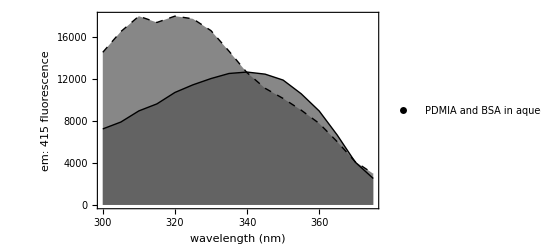

```mathematica
ListLinePlot[{exPDMIABSA[[1]],exPDMIAwater[[1]]},PlotStyle->{Black,Directive[Dashed,Black]},AxesOrigin->{exPDMIABSA[[1]][[1,1]],0},Joined->True,Filling->Axis,FillingStyle->Directive[Opacity[0.7],Darker[Gray]],PlotRange->{{exPDMIABSA[[1]][[1,1]],exPDMIABSA[[1]][[-1,1]]},{0,All}},Frame->True,FrameLabel->{{"em: 415 \nfluorescence",""},{"wavelength (nm)",""}},LabelStyle->18,PlotLegends->SwatchLegend[{"PDMIA and BSA in aqueous buffer",dpdmia},LegendMarkers->marker,LegendMarkerSize->{40,20}]]
```

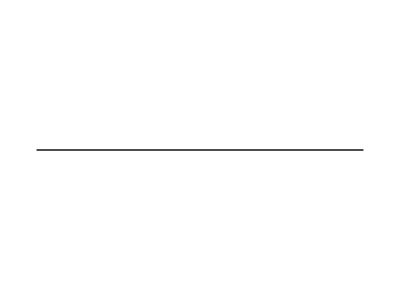

```mathematica
marker=Graphics[Line[{{0,0},{1,0}}],ImageSize->Tiny]
```

```mathematica
data1=exPDMIABSA[[1]];
data2=exPDMIAwater[[1]];
exportPDFMultiSpectrumF["exPDMIAwater","PDMIA in water","exPDMIABSA","PDMIA reacted with BSA in aqueous buffer"]
```

FexPDMIABSAexPDMIAwater.pdf

```mathematica
exportPDFMultiSpectrumF["emPDMIABSA320","PDMIA and BSA in aqueous buffer","emPDMIAwater320","PDMIA in water"]
```

FemPDMIAwater320emPDMIABSA320.pdf

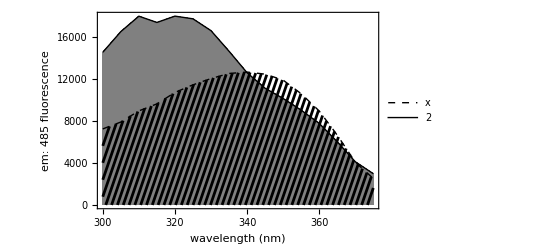

```mathematica
makeMultiFluorPlot[data1,"x",data2,"2","em: 485"]
```

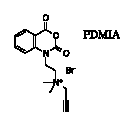

```mathematica
dpdmia
```

```mathematica
ddmia=Import["/Users/Tommy/Documents/UNC Charlotte/Research with Ogle/5 Thesis/figures/ddmia.pdf"][[1]]
```

-Graphics-

```mathematica
dracia
```

-Graphics-